# Moving point heat source

In this short notice we explore solution to moving heat source given by the paper “Solutions for modelling moving heat sources in semi-infinite medium and applications to laser material processing”
by M.Van Elsen, M.Baelmans, P.Mercelis, J.-P.Kruth  doi:10.1016/j.ijheatmasstransfer.2007.02.044.

Moving point heat source in 3 D semi-inifite body is described by Carslaw and Jaeger:
k  conductivity (W/mK)
T0   room temperature (K)
Tm melting temperature (K)
V scan speed (m/s)
x coordinate along scanning direction (m)
y coordinate perpendicular to scanning direction (m)
z coordinate in depth (m)
P laser power (W)

Values of thermal parameters for Ti - 6 Al - 4 V

In the paper by M.Van Elsen the Eq.(5) there is type error it should be:
θ = P_L/(2 π k R(T-T_o))exp(-V(R+x)/2κ)

```mathematica
Tm=1933;
T0=293;
k=6.0;
κ =2.4 10^-6;
```

```mathematica
θ[P_,κ_,V_,x_,y_,z_]:= P/(2 π k √(x^2+y^2+z^2)(Tm-T0)) Exp[-V(√(x^2+y^2+z^2)+x)/(2 κ)];
```

Result for moving point source

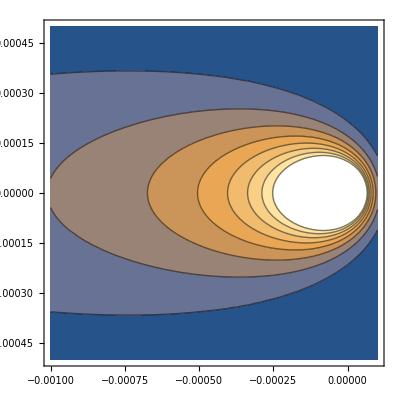

```mathematica
ContourPlot[θ[25.0,κ,0.05,x,y,0.0],{x,-10 10^-4,1 10^-4},{y,-5 10^-4,5 10^-4}]
```

These are results for Uniform moving heat source:
The solution is given by M.Van Elsen et al. International Journal of Heat and mass transfer.
50 (2007) 4872-4882.

Definition of the Fourier number:
Fo = (diffusive transport rate)/(storage rate)=αt/L^2

The additional material parameters for uniform source term are:

```mathematica
ρ = 4450; (*density in kg/m^3 *)
cp = 546;(* specific heat in J/kg K *)
k = 6 ; (*conductivity W/m K *)
ah =ch = 0.000075; (* laser dimension in m *)
bh = 0.00005; (* laser dimension in m *)
```

```mathematica
Fos[κ_,s_,t_]:=(κ t)/s^2
```

```mathematica
η [P_,ρ_,cp_,ah_,bh_,ch_,Tm_,To_,t_]:=ρ cp ah bh ch (Tm-To)/(P t);
```

```mathematica
Erfh[κ_,x_,s_,tp_]:=Erf[(√Fos[κ,s,tp])/2(x/s-1)]-Erf[(√Fos[κ,s,tp])/2(x/s+1)]
θunif[P_,κ_,V_,x_,y_,z_,t_]:=-1/(2^5 η[P,ρ,cp,ah,bh,ch,Tm,T0,t])NIntegrate[Erfh[x+V(t-tp),ch,tp]*Erfh[y,ah,tp]*Erfh[z,bh,tp], {tp,0,t}]
```

#### in original paper the Fo is seems defined as s^2/κ(t-t')

```mathematica
mErfh[κ_,x_,s_,t_,tp_]:=Erf[(x-s)/(√(4 κ(t-tp)))]-Erf[(x+s)/(√(4 κ(t-tp)))];
```

```mathematica
mθ[P_,κ_,V_,x_,y_,z_,t_]:=-P/(2^5 ρ ah bh ch (Tm-T0))NIntegrate[mErfh[κ,x+V(t-tp),ch,t,tp] *mErfh[κ,y,ah,t,tp]*mErfh[κ,z,bh,t,tp], {tp,0,t},MinRecursion-> 2]
```

```mathematica
funx[x_,y_,z_,time_]:=-25/(2^5 ρ cp ah bh ch (Tm-T0))NIntegrate[mErfh[κ,x+0.05(time-tp),ch,time,tp]*mErfh[κ,y,ah,time,tp]*mErfh[κ,z,bh,time,tp] ,{tp,0,time},MinRecursion-> 2]
```

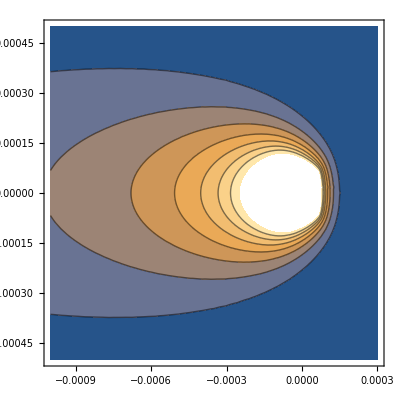

```mathematica
ContourPlot[funx[x,y,0.0,10],{x,-10 10^-4,3 10^-4},{y,-5 10^-4,5 10^-4}]
```

3d plot of the uniform moving source:

```mathematica
Plot3D[funx[x,y,0.0,10],{x,-10 10^-4,1 10^-4},{y,-5 10^-4,5 10^-4},PlotRange->{0,3}]
```

-Graphics3D-

Some specific cross sections of this solutions are:

```mathematica
FindMaximum[funx[x-0.000101099,0,0.,10],
```

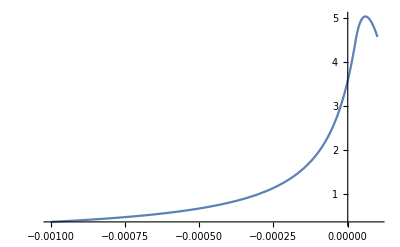

```mathematica
Plot[funx[x-0.000101099,0,0.0,10],{x,-10 10^-4,1 10^-4}, PlotRange->All]
```

and for x=0 we have:

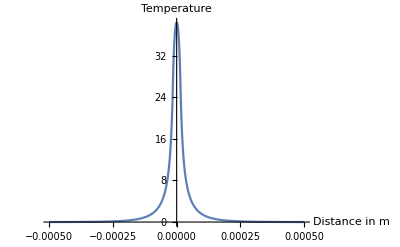

```mathematica
Plot[funx[0,y,0.0,10],{y,-5 10^-4,5 10^-4}, PlotRange->All,AxesLabel->{"Distance in m", "Temperature"}]
```

Read the data obtained numerically:

```mathematica
data=Drop[Drop[Import["Y:\\TestCases\\temperature-Ti6Al4V","Table"],4],-5]
```

{{0.,74591.1},{0.02,74733.5},{0.04,74888.4},{0.06,75057.9},{0.08,75244.6},{0.1,75452.},{0.12,75684.5},{0.14,75948.1},{0.16,76250.5},{0.18,76602.7},{0.2,77019.9},{0.22,77523.9},{0.24,78144.},{0.26,78915.3},{0.28,79503.8},{0.3,79944.3},{0.32,80265.5},{0.34,80487.9},{0.36,80625.},{0.38,80685.4},{0.4,80673.7},{0.42,80591.4},{0.44,80437.2},{0.46,80206.5},{0.48,79891.},{0.5,79477.2},{0.52,78944.7},{0.54,78264.9},{0.56,77403.},{0.58,76692.4},{0.6,76097.9},{0.62,75590.},{0.64,75147.},{0.66,74753.7},{0.68,74399.2},{0.7,74075.6},{0.72,73777.1},{0.74,73499.3},{0.76,73238.6}}

```mathematica
data[[ Position[data,Max[data]][[1,1]] ,1]]
```

0.38

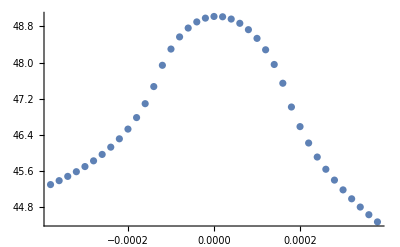

```mathematica
fig1=ListPlot[Map[{#[[1]] 10^-3-data[[ Position[data,Max[data]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,data] ]
```

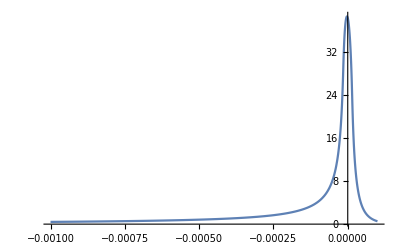
```mathematica
Show[-Graphics-,-Graphics-]
```

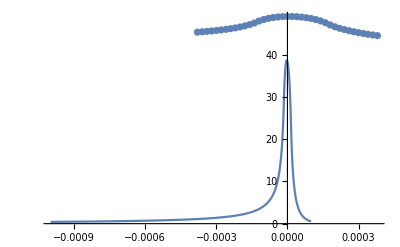

```mathematica
data1=Drop[Drop[Import["Y:\\TestCases\\temperature-BC","Table"],3],-4]
```

{{0.,2473.16},{0.02,2926.69},{0.04,3501.93},{0.0599999,4235.39},{0.0799999,4795.08},{0.0999999,5217.11},{0.12,5530.93},{0.14,5757.46},{0.16,5910.49},{0.18,5998.67},{0.2,6026.77},{0.22,5996.37},{0.24,5906.02},{0.26,5751.06},{0.28,5523.01},{0.3,5208.2},{0.32,4785.86},{0.34,4226.57},{0.36,3494.05},{0.38,2919.93},{0.4,2467.46},{0.42,2106.2},{0.44,1813.84},{0.46,1574.6}}

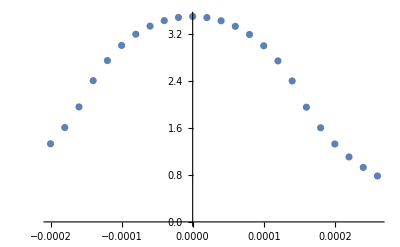

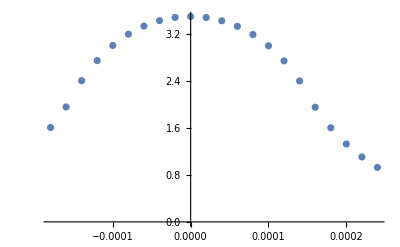

```mathematica
fig2=ListPlot[Map[{#[[1]] 10^-3-data1[[ Position[data1,Max[data1]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,data1] ]
```

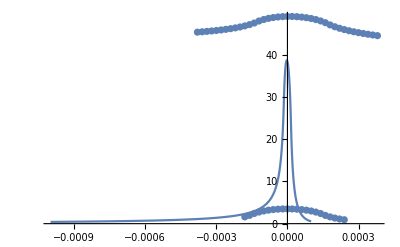

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

```mathematica
data2=Drop[Drop[Import["Y:\\TestCases\\temperature-75BC-corr2","Table"],4],-4]
```

{{0.0200032,1212.2},{0.0400063,1260.81},{0.0600096,1313.1},{0.0800128,1369.41},{0.100016,1430.08},{0.120019,1495.45},{0.140022,1565.92},{0.160025,1641.88},{0.180029,1723.76},{0.200032,1812.04},{0.220035,1907.26},{0.240038,2010.06},{0.260041,2121.22},{0.280045,2241.66},{0.300048,2372.55},{0.320051,2515.37},{0.340054,2671.97},{0.360057,2844.71},{0.380061,3036.65},{0.400064,3251.89},{0.420067,3496.04},{0.44007,3777.21},{0.460073,4107.6},{0.480077,4506.13},{0.50008,5002.79},{0.520083,5645.56},{0.540086,6515.42},{0.560089,7773.25},{0.580092,9771.56},{0.600095,10424.8},{0.620099,10359.3},{0.640102,9871.81},{0.660105,9072.75},{0.680108,7971.9},{0.700112,6504.22},{0.720115,4573.78},{0.740118,2378.97},{0.760121,1374.05},{0.780124,880.76},{0.800127,622.285},{0.82013,481.383},{0.840134,402.507},{0.860137,357.474},{0.88014,331.37},{0.900143,316.046},{0.920146,306.954},{0.94015,301.508},{0.960153,298.219},{0.980156,296.219},{1.00016,294.995},{1.02016,294.241},{1.04017,293.775},{1.06017,293.485},{1.08017,293.305},{1.10018,293.192},{1.12018,293.121}}

```mathematica
Max[data2]
```

Max[10378.5,_temp_1,X]

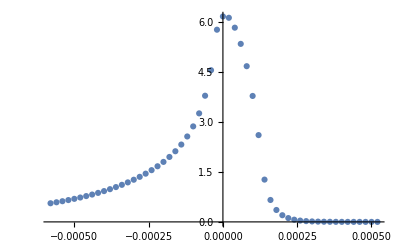

```mathematica
fig3=ListPlot[Map[{#[[1]] 10^-3-data2[[ Position[data2,Max[data2]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,data2]]
```

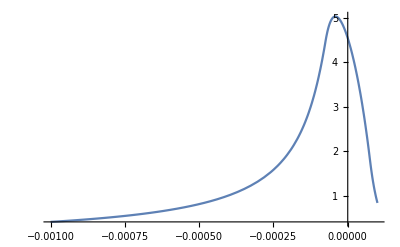
```mathematica
Show[fig3,-Graphics-]
```

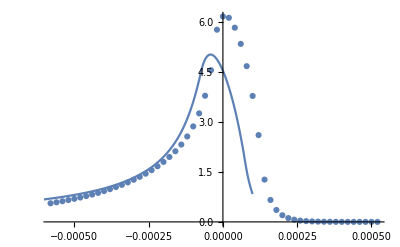

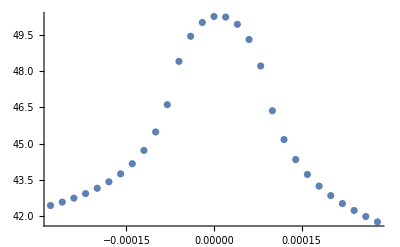
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,fig3]
```

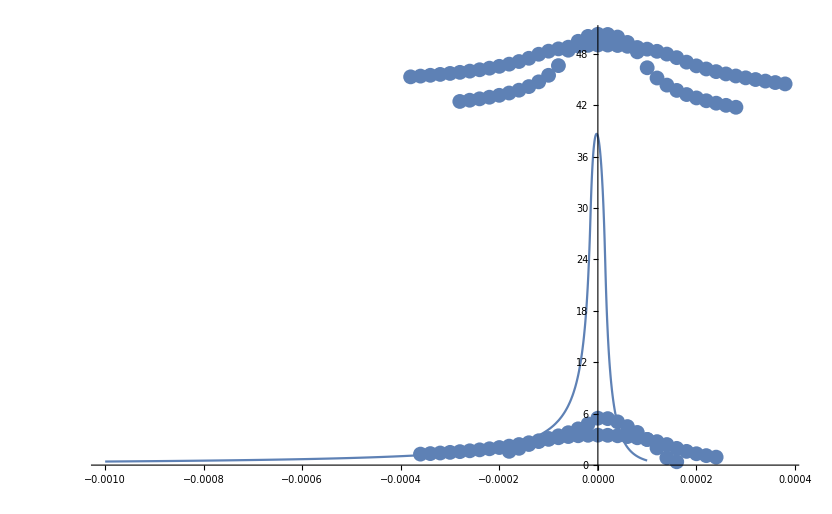

Implementation of the semi-ellipsoidal moving heat source:
The result in dimensional form is given by:
θ/n=1/(√(2π))∫_0^((V^2 t)/(2κ)) 1/(√(τ+u_a^2)√(τ+u_b^2))(A_1/(√(τ+u_c^2)))ⅆτ

Nondimensional variables using Christensen method:

```mathematica
ξ[x_]:=V x /(2 κ);
ψ[y_]:= V y/(2 κ);
ζ[z_]:= V z/(2 κ);
τ[t_]:= V^2 (t-tp)/(2 κ);
ua=V ah 2 √6 κ; uc=V ch 2 √6 κ;
ub=V bh 2 √6 κ; n=P V/(4 π κ^2 ρ cp(Tm-T0));
```

```mathematica
A1[x_,y_,z_,t_] :=Exp[(-(ξ[x]+τ[t])^2)/(2(τ[t]+uc^2))-□/□]
```